```mathematica
Clear["Global`*"]
```

## Example 1D system

In light of Halatek & Frey (Nat Phys 2018), what we need here is a mechanism for lateral instability, that allows the creation of a spatially non-trivial pattern. Instead of starting with a non-trivial pattern, can we generate spatial non-uniformity starting from a uniform configuration?
( Test with activator - inhibitor model )
* Note that mass is not conserved in our model

Question: for R[c_]:= k c^n/(Keq^n+c^n)- γ c; with bistability (n=2), when does the system become spatially uniform?

```mathematica
(* R[c_]:= k c^2/(Keq^2+c^2) - γ c; *)
R[c_]:= k c^n/(Keq^n+c^n)- γ c;
f[x]:= Sin[(4 π)/L x];
L=10;
tmax=10; 
params={d-> 1, k-> 1.2, γ-> 1, Keq-> 0.5, n-> 100};
sol=First@NDSolveValue[{D[c[x,t], t] == d D[c[x,t], {x,2}] + R[c[x,t]] /.params, c[0,t]==c[L,t], c[x,0]==f[x]}, {c}, {x,0,L},{t,0,tmax}]
```

InterpolatingFunction[{{…, 0., 10., …}, {0., 10.}}, <>]

```mathematica
Plot3D[sol[x,t], {x,0,L}, {t,0,tmax}, AxesLabel-> {"x", "t", "c[x,t]"}, PlotRange-> All]
```

-Graphics3D-

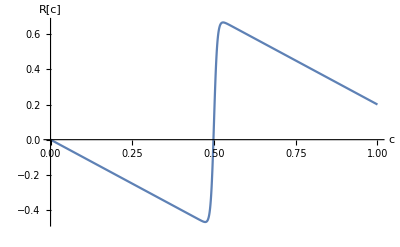

```mathematica
Plot[R[c]/. params, {c,0,1}, AxesLabel-> {"c", "R[c]"}]
```

Steady state solution (probably not well-defined, depends on initial conditions)

InterpolatingFunction[{{0., 10.}}, <>]

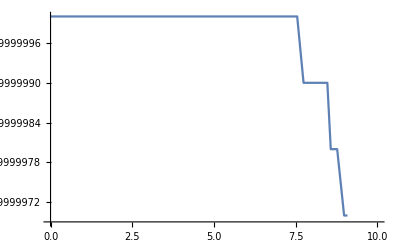

```mathematica
c0= 1;
Lorentz[x_]:=1/(g π)g^2/(Min[(L/2-x)^2,x^2]  + g^2)/. {g->0.001}; (*Lorentzian*)
solss=First@NDSolveValue[{0==( d D[c[x], {x,2}] + k  - γ c[x] )/.params, c[0]==c[L], c'[0]==c'[L]}, {c}, {x,0,L}]
Plot[solss[x], {x,0,L}]
```